## Mathematica dealing with rho from matlab

### Importing cr, cf, and cl1 from Mat bt matlab

```mathematica
rho500dim2=Import["E:\\06_Coh\\00_Code\\00_dim2gs\\00_data\\a0_20191012_rho2_10000.mat"];
CC500dim2=Import["E:\\06_Coh\\00_Code\\00_dim2gs\\00_data\\a0_20191012_cc_10000.mat"];purity500dim2=Import["E:\\06_Coh\\00_Code\\00_dim2gs\\00_data\\a0_20191012_purity_10000.mat"];
rhodim2a=Flatten[rho500dim2,1 ];
(*rhodim2=Flatten[rhodim2a,2];*)
Dimensions[rhodim2a]
rhodim2a[[1]]
Abs[rhodim2a[[1]][[1,2]]]
(*Dimensions[rhodim2a]
Dimensions[Flatten[rhodim2a,1]]*)

CCdim2a=Flatten[CC500dim2,1];
CCdim2=Flatten[CCdim2a,2];
Dimensions[Flatten[CCdim2,1]]
puritydim2a=Flatten[purity500dim2,1];
puritydim2=Flatten[puritydim2a,2];
Dimensions[Flatten[puritydim2,1]]
```

{10000,2,2}

{{0.489116+0. ⅈ,-0.131459+0.145311 ⅈ},{-0.131459-0.145311 ⅈ,0.510884+0. ⅈ}}

0.195951

{10000}

{10000}

#### Search the density matrix where |rho10|>|rhoii|

```mathematica
rhodim2a;
For[i=1;t=x,i<50,i++,t=t^2+i;If[Abs[rhodim2a[[i]][[1,2]]]>rhodim2a[[i]][[1,1]]||Abs[rhodim2a[[i]][[1,2]]]>rhodim2a[[i]][[2,2]],{Print[{{序号}{i}}],Print[rhodim2a[[i]]],Print[ 文章程序计算结果],Print[ Flatten[CCdim2,1][[i]]],rhotmp=Inverse[rhodim2a[[i]]],ss=If[Re[rhotmp[[1,1]]]≤Re[rhotmp[[2,2]]],Re[rhotmp[[1,1]]],Re[rhotmp[[2,2]]]],Print[ 解析式计算结果],Print[1-1/ss],Print[ 2abs(rho12)],Print[2Abs[rhodim2a[[i]][[1,2]]]]},Indeterminate]]
```

{{5 序号}}

{{0.654603+0. ⅈ,-0.330807-0.229676 ⅈ},{-0.330807+0.229676 ⅈ,0.345397+0. ⅈ}}

文章程序计算结果

0.814955

解析式计算结果

0.814955

2 abs rho12

0.805441

{{13 序号}}

{{0.102223+0. ⅈ,0.0163516-0.236249 ⅈ},{0.0163516+0.236249 ⅈ,0.897777+0. ⅈ}}

文章程序计算结果

0.650834

解析式计算结果

0.650834

2 abs rho12

0.473627

{{14 序号}}

{{0.826078+0. ⅈ,0.173229-0.225454 ⅈ},{0.173229+0.225454 ⅈ,0.173922+0. ⅈ}}

文章程序计算结果

0.638716

解析式计算结果

0.638716

2 abs rho12

0.56864

{{17 序号}}

{{0.382168+0. ⅈ,-0.232815+0.319163 ⅈ},{-0.232815-0.319163 ⅈ,0.617832+0. ⅈ}}

文章程序计算结果

0.790543

解析式计算结果

0.790543

2 abs rho12

0.790108

{{19 序号}}

{{0.743765+0. ⅈ,-0.0601584+0.290221 ⅈ},{-0.0601584-0.290221 ⅈ,0.256235+0. ⅈ}}

文章程序计算结果

0.599074

解析式计算结果

0.599074

2 abs rho12

0.592781

{{23 序号}}

{{0.719991+0. ⅈ,-0.19666-0.276403 ⅈ},{-0.19666+0.276403 ⅈ,0.280009+0. ⅈ}}

文章程序计算结果

0.690974

解析式计算结果

0.690974

2 abs rho12

0.678451

{{27 序号}}

{{0.261827+0. ⅈ,0.0642557-0.293208 ⅈ},{0.0642557+0.293208 ⅈ,0.738173+0. ⅈ}}

文章程序计算结果

0.605945

解析式计算结果

0.605945

2 abs rho12

0.600332

{{30 序号}}

{{0.107208+0. ⅈ,0.0203928-0.165134 ⅈ},{0.0203928+0.165134 ⅈ,0.892792+0. ⅈ}}

文章程序计算结果

0.365446

解析式计算结果

0.365446

2 abs rho12

0.332778

{{31 序号}}

{{0.180803+0. ⅈ,-0.198355-0.286076 ⅈ},{-0.198355+0.286076 ⅈ,0.819197+0. ⅈ}}

文章程序计算结果

0.851059

解析式计算结果

0.851059

2 abs rho12

0.696231

{{32 序号}}

{{0.755222+0. ⅈ,0.217829-0.19799 ⅈ},{0.217829+0.19799 ⅈ,0.244778+0. ⅈ}}

文章程序计算结果

0.59877

解析式计算结果

0.59877

2 abs rho12

0.588725

{{34 序号}}

{{0.0804427+0. ⅈ,-0.138254-0.203053 ⅈ},{-0.138254+0.203053 ⅈ,0.919557+0. ⅈ}}

文章程序计算结果

0.830601

解析式计算结果

0.830601

2 abs rho12

0.491303

{{37 序号}}

{{0.256396+0. ⅈ,-0.103521-0.278568 ⅈ},{-0.103521+0.278568 ⅈ,0.743604+0. ⅈ}}

文章程序计算结果

0.600851

解析式计算结果

0.600851

2 abs rho12

0.594363

{{39 序号}}

{{0.753739+0. ⅈ,-0.0693301-0.273748 ⅈ},{-0.0693301+0.273748 ⅈ,0.246261+0. ⅈ}}

文章程序计算结果

0.570082

解析式计算结果

0.570082

2 abs rho12

0.564781

{{41 序号}}

{{0.800926+0. ⅈ,0.288948+0.223474 ⅈ},{0.288948-0.223474 ⅈ,0.199074+0. ⅈ}}

文章程序计算结果

0.869335

解析式计算结果

0.869335

2 abs rho12

0.730565

{{44 序号}}

{{0.360449+0. ⅈ,-0.0583211+0.358378 ⅈ},{-0.0583211-0.358378 ⅈ,0.639551+0. ⅈ}}

文章程序计算结果

0.726205

解析式计算结果

0.726205

2 abs rho12

0.726185

{{47 序号}}

{{0.776525+0. ⅈ,-0.124186-0.312801 ⅈ},{-0.124186+0.312801 ⅈ,0.223475+0. ⅈ}}

文章程序计算结果

0.730318

解析式计算结果

0.730318

2 abs rho12

0.673102

#### Search the

```mathematica
rhodim2a;
For[i=1;t=x,i<10000,i++,t=t^2+i;If[2Flatten[puritydim2,1][[i]]-1< (Flatten[CCdim2,1][[i]])^2,{Print[{{序号}{i}}],Print[rhodim2a[[i]]],Print[ 文章程序计算结果],Print[ Flatten[CCdim2,1][[i]]]},Indeterminate]]
```

#### Search the Cw where Cw < 2|rho01|

```mathematica
rhodim2a;
For[i=1;t=x,i<50,i++,t=t^2+i;If[2 Abs[rhodim2a[[i]][[1,2]]]> Flatten[CCdim2,1][[i]]+10^(-10),{Print[{{序号}{i}}],Print[rhodim2a[[i]]],Print[2 Abs[rhodim2a[[i]][[1,2]]]],Print[ 文章程序计算结果],Print[ Flatten[CCdim2,1][[i]]]},Indeterminate]]
```

```mathematica
f=1-(1-(x^2+a^2))/(2(1-x))-0.5;
df=D[f,x]
df2=D[df,x]
NSolve[df==0,x]
df/.x->1
```

x/(1-x)-(1-a^2-x^2)/(2 (1-x)^2)

1/(1-x)+(2 x)/(1-x)^2-(1-a^2-x^2)/(1-x)^3

{{x→1.-1. a},{x→1.+a}}

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Indeterminate

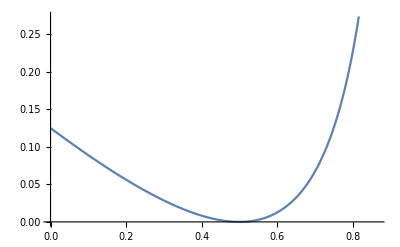

```mathematica
Plot[f/.a->0.5,{x,0,√(1-0.5^2)}]
```

#### CR versus Cl1

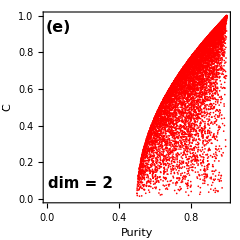

```mathematica
dim =2;
clcrd2=Transpose[{puritydim2,CCdim2}];
fig001d2=ListPlot[clcrd2,PlotRange->{{0,1.},{0,1.}},Frame->True,FrameStyle->{{Thick,Thick},{Thick,Thick}},PlotStyle->{{Red,Thick,PointSize[0.005]}},LabelStyle->{15,Bold},FrameLabel->{Style["Purity",FontSize->16],Style["C̄",FontSize->16]},FrameTicksStyle->Directive[12.5],Epilog->{Text[Style["(e)",FontSize->16,FontWeight->"Bold"],Scaled[{.08,.92}]],Text[Style["dim = 2",FontSize->15,FontWeight->"Bold"],Scaled[{.2,.1}]](*,Text[Style["y = (x+1)/3",FontSize->18,FontWeight->"Bold"],Scaled[{.7,.85}]]*)},ImageSize->{240,240},AspectRatio->1,GridLines->{{1/dim},None},GridLinesStyle->Directive[Blue,Dashed]]
(*fig002d3=Plot[{x},{x,0,1.05},PlotRange->{{0,1.05},{0,1.05}},PlotStyle->{{Thickness[0.005],Darker[Green],Dashed}}];(* d1 is dim *)
figdim3=Show[fig001d3,fig002d3]*)
```

```mathematica
Dimensions[rho500dim2];
rho1=rho500dim2[[1,1]];
2Abs[rho1[[1,2]]]
CCdim2[[1]]
puritydim2[[1]];
```

0.391902

0.391902

```mathematica
Dimensions[rho500dim2];
rho2=rho500dim2[[1,2]];
2Abs[rho2[[1,2]]]
CCdim2[[2]]
puritydim2[[2]];
```

0.427944

0.427944

```mathematica
Dimensions[rho500dim2]
rho1000=rho500dim2[[1,1000]]
CCdim2[[1000]]
puritydim2[[1000]]
```

{1,10000,2,2}

{{0.43658+0. ⅈ,0.455549-0.120206 ⅈ},{0.455549+0.120206 ⅈ,0.56342+0. ⅈ}}

0.94502

0.951994

```mathematica
rho1000=rho500dim2[[1,1000]]
Inverse[rho1000]
```

{{0.43658+0. ⅈ,0.455549-0.120206 ⅈ},{0.455549+0.120206 ⅈ,0.56342+0. ⅈ}}

{{23.4727-2.47051×10^-15 ⅈ,-18.9787+5.00793 ⅈ},{-18.9787-5.00793 ⅈ,18.1884-2.87332×10^-15 ⅈ}}

```mathematica
1-1/18.1884//N
```

0.94502

```mathematica
2Abs[rho1000[[1,2]]]
```

0.942284